# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Plateu\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
cp=ResourceFunction["CombinePlots"];
```

```mathematica
Clear[Isingnoisy];
Isingnoisy[h_,g_,J_,L_] := Module[{NNIndices,A,B,ϵ=RandomVariate[NormalDistribution[0,1],L]},
NNIndices=Normal[SparseArray[Thread[{#,#+1}->3],{L}]&/@Range[L-1]];
A=-Normal[Total[{h*Pauli[#]+g*Pauli[3#]&/@IdentityMatrix[L],J*(Pauli/@NNIndices)},2]];
B=0.001*ϵ. (Pauli/@DiagonalMatrix[ConstantArray[1,L]]);
A+B];

Clear[arrayt];
(*arrayt[t_,val_]:=arrayt[t,val]=Exp[-I*val*t];*)
arrayt[t_,val_]:=arrayt[t,val]=Exp[-I*val*t];
Clear[new];
new[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=ArrayReshape[N[Total[ phases*ck]],{a,a}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
Clear[purity];
purity[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=ArrayReshape[N[Total[ phases*ck]],{a,a}];
Total[(Chop[SingularValueList[psit]])^4]
];
Clear[survival];
survival[ini_,t_,val_,vec_]:=Module[{inieigen=Conjugate[vec].ini,phases=Chop[arrayt[t,val]]*vec},
Quiet[Abs[Conjugate[ini].Total[inieigen*phases]]^2]
];

Clear[schmidt];
schmidt[ini_,t_,La_,val_,vec_]:=Module[{rho,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=N[Total[ phases*ck]];
rho=MatrixPartialTrace[Dyad[psit],2,{a,a}];
Sort[Chop[Eigenvalues[rho]]]
];
```

# T1

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=10^-1.5;
h=1.;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

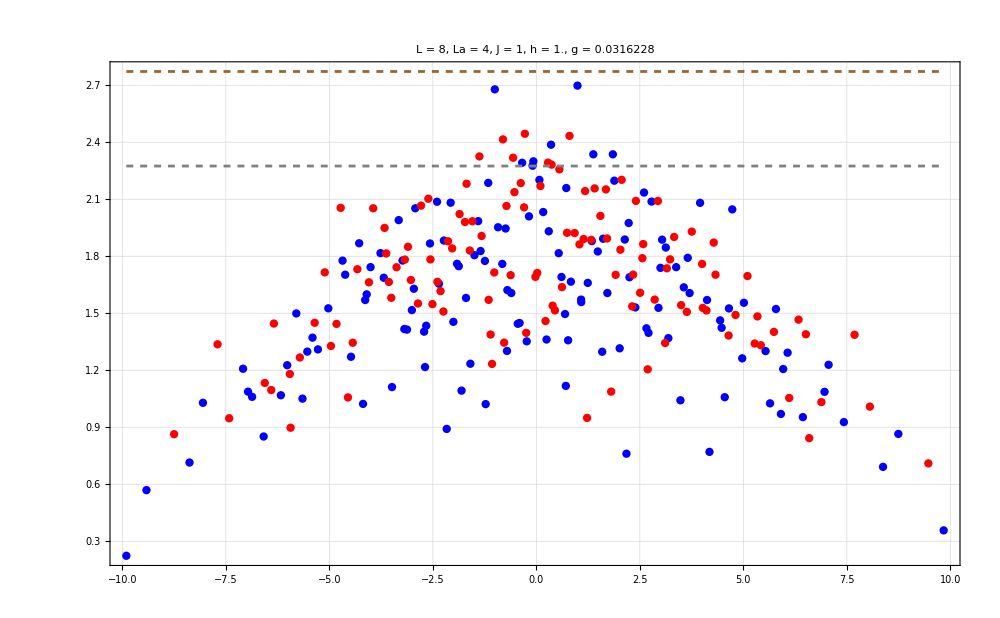

```mathematica
Show[{ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]],Plot[{N[pageEntropy[L/2,L/2]],Log[2^(L/2)]},{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Dashed,Gray],Directive[Dashed,Brown]},PlotRange->All]},PlotRange->All]
```

# SVD

```mathematica
tlist=Table[10^i,{i,-1,6,0.005}];
tlist//Length
```

1401

```mathematica
productstatesfull=Table[RandomChainProductState[L],{i,2}];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,2}];
```

```mathematica
entropydata=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

```mathematica
puritydata=ParallelTable[{t,purity[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

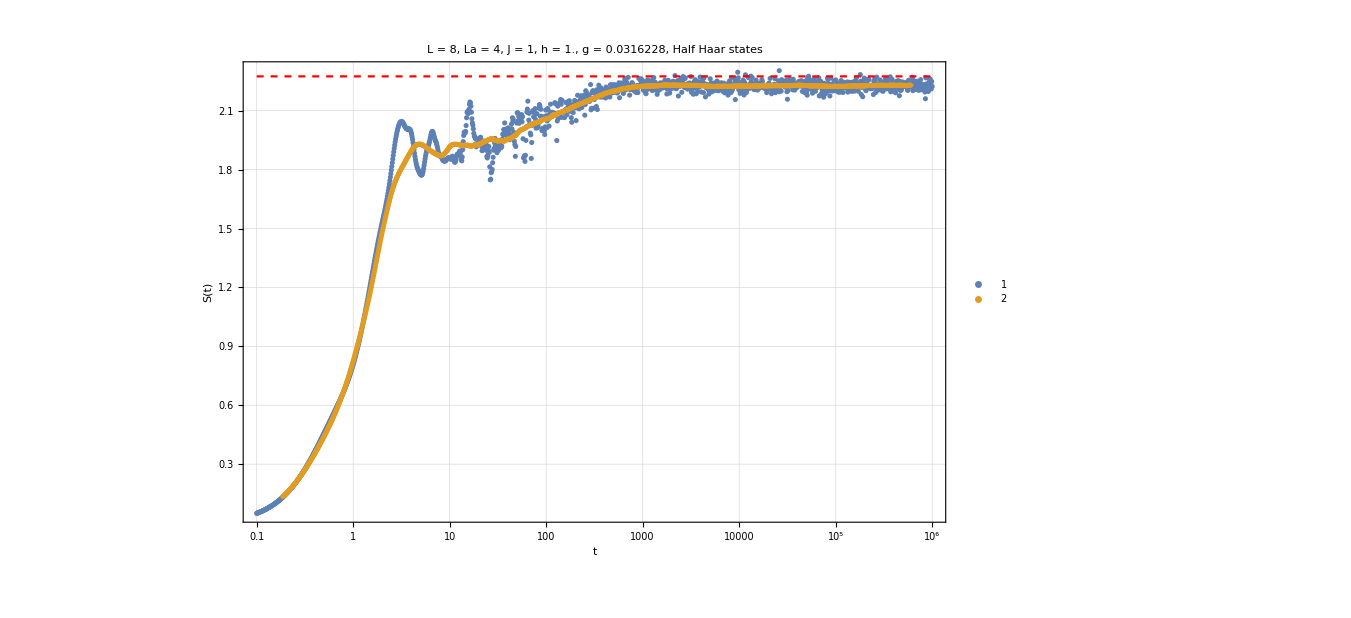

```mathematica
entropyplot=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

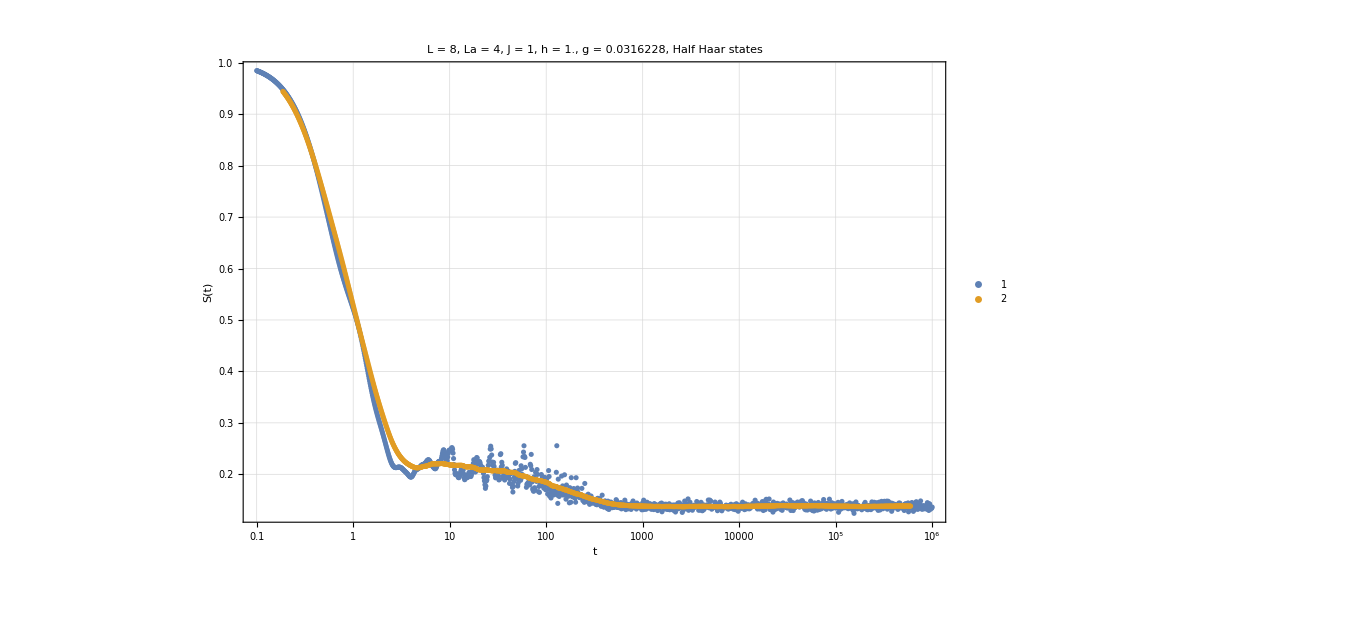

```mathematica
purityplot=Show[{ListLogLinearPlot[{Mean[puritydata],MovingAverage[Mean[puritydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic]},PlotRange->All]
```

## Survival probatility

```mathematica
(*productstatesfull=Table[haar[L],{i,5}];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,5}];*)
```

```mathematica
survivaldata=ParallelTable[{t,survival[j,t,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

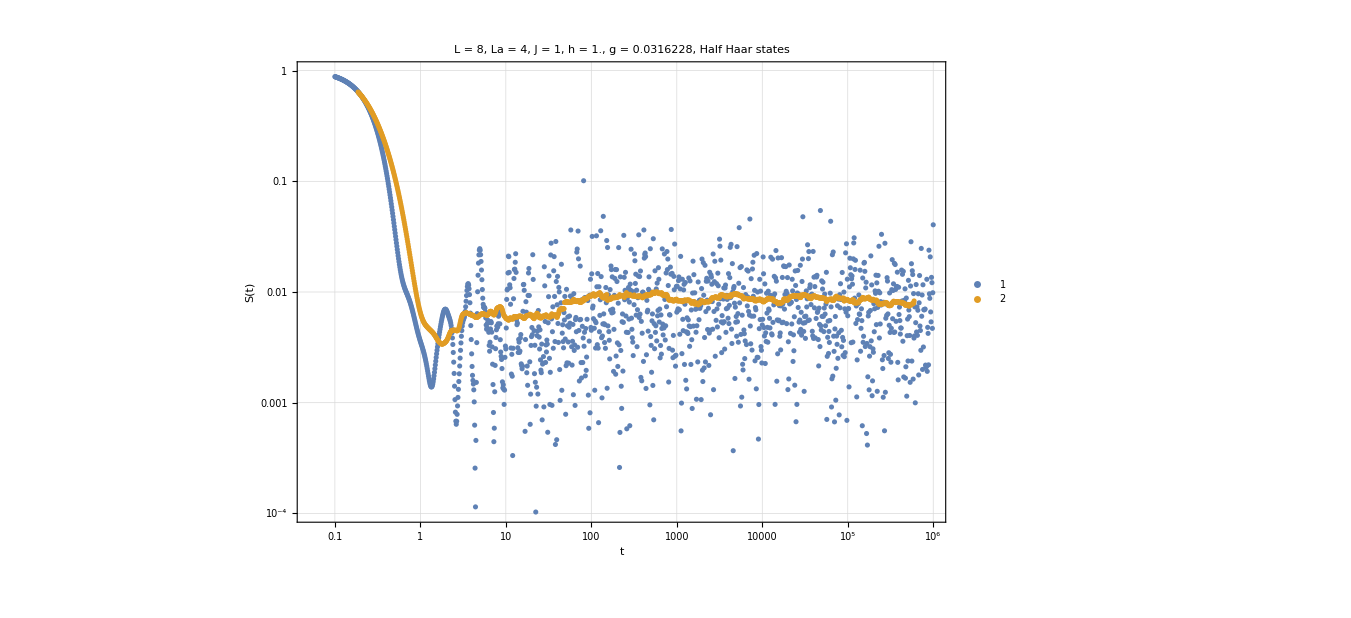

```mathematica
survivalplot=ListLogLogPlot[{Mean[survivaldata],MovingAverage[Mean[survivaldata],100]},PlotRange->{All,{10^-4,1}},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic]
```

## Spectrum

```mathematica
values=ParallelTable[schmidt[productstatesfull[[1]],t,La,allvals,allvecs],{t,tlist},DistributedContexts->Full];
```

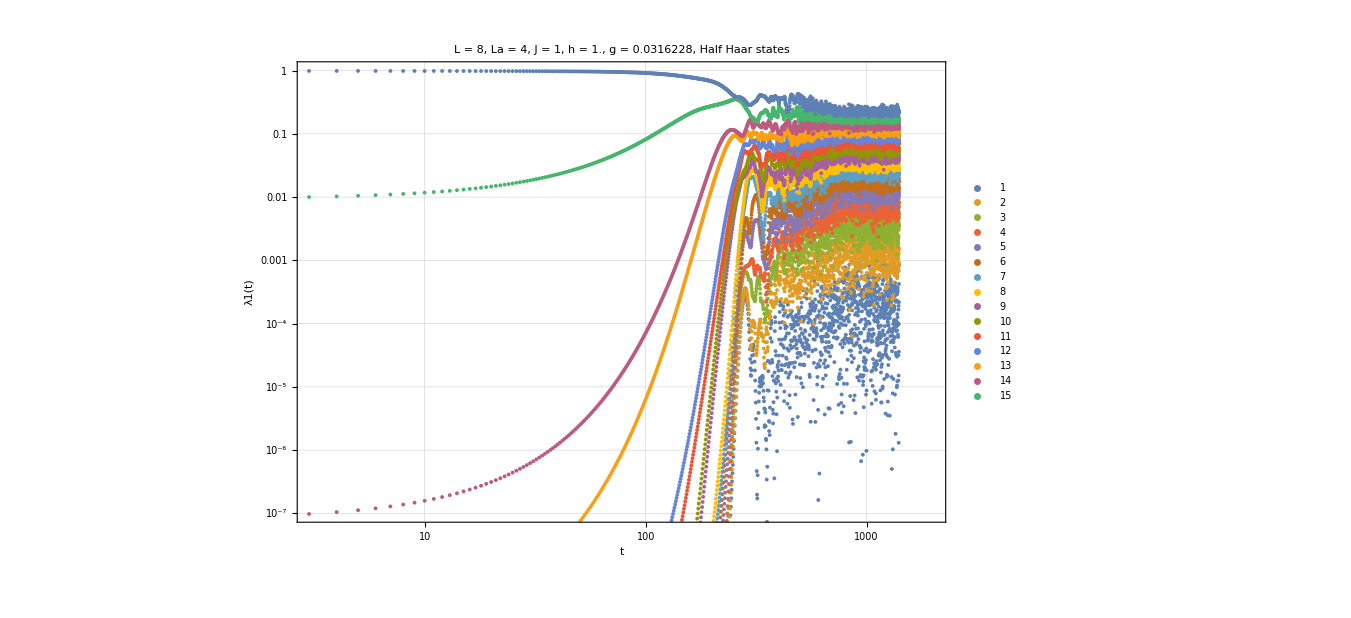

```mathematica
ListLogLogPlot[Transpose[values],Joined->False,PlotRange->{{0,2000},{10^-7,1}},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotLegends->Automatic]
```

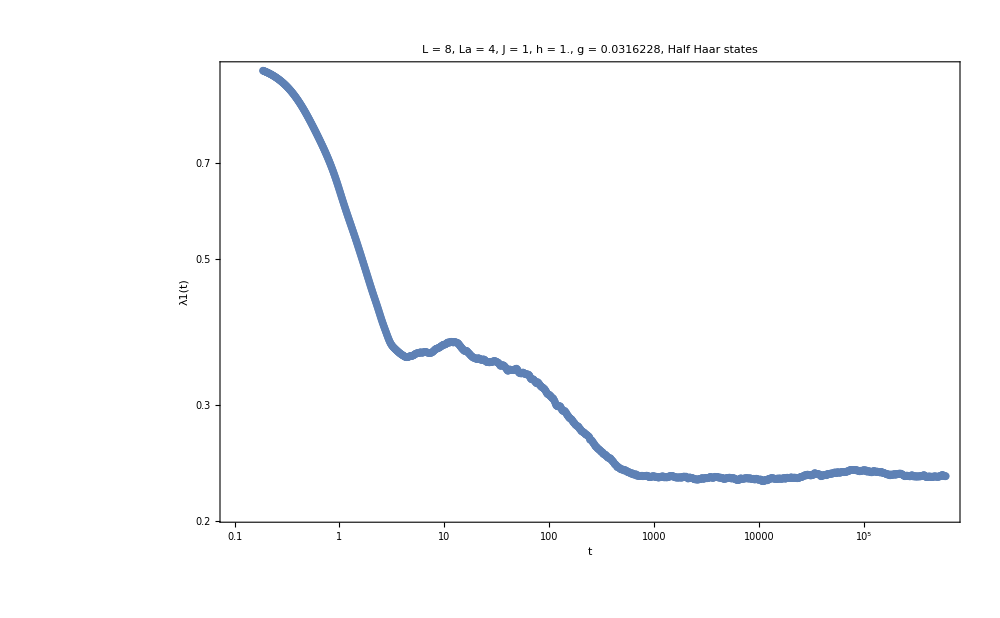

```mathematica
plot1=ListLogLogPlot[MovingAverage[Transpose[{tlist,Transpose[values][[-1]]}],100],PlotRange->All,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotLegends->Automatic]
```

```mathematica
plots={};
```

```mathematica
AppendTo[plots,plot2];
```

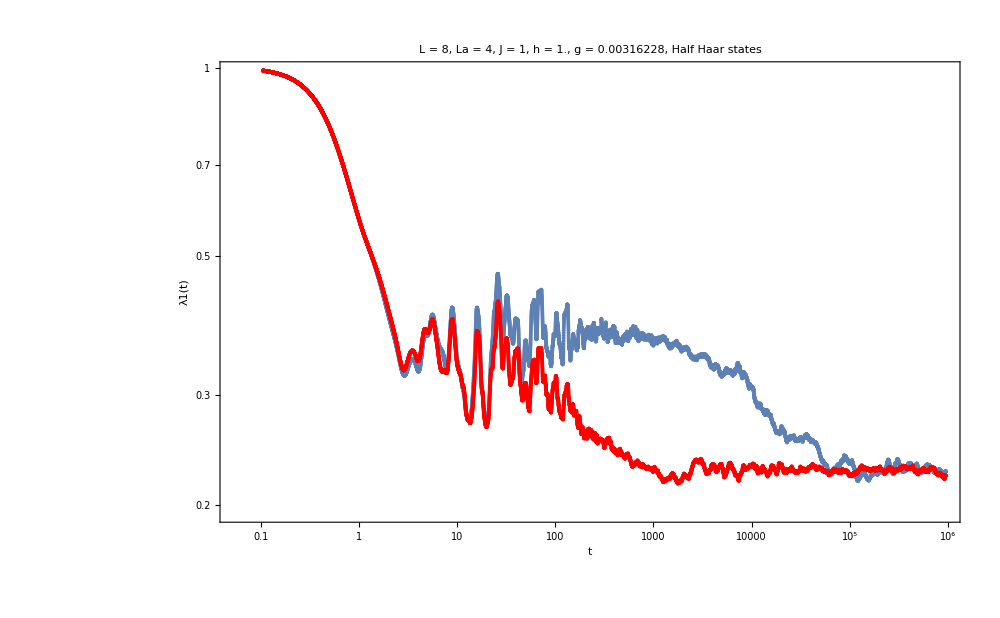

```mathematica
Show[plots]
```

# g -> 0, Largest schmidt

```mathematica
J=1;
h=1;
glist=Table[10^i,{i,-5,0,0.3}];
n=Length[glist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

18

```mathematica
tlist=Table[10^i,{i,-1,4,0.002}];
tlist//Length
```

2501

```mathematica
c=N[pageEntropy[L/2,L/2]];
```

```mathematica
productstatesfull=Flatten[KroneckerProduct[haar[L/2],haar[L/2]]];
```

```mathematica
alldata1={};
alldata2={};
Do[

H=IsingNNOpenHamiltonian[glist[[g]],0,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

values=ParallelTable[schmidt[productstatesfull,t,La,allvals,allvecs],{t,tlist},DistributedContexts->Full];
AppendTo[alldata1,MovingAverage[Transpose[{tlist,Transpose[values][[-1]]}],100]];
AppendTo[alldata2,MovingAverage[Transpose[{tlist,Transpose[values][[-2]]}],100]];

,{g,Length[glist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata1,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},{0.2,0.5}}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata2,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ2(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata1,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-4,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},{0.2,1}}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata2,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ2(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-4,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata1,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-4,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},{0.2,1}}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata2,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["λ2(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-4,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

# g -> 0, Plateu

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
h=1;
glist=Table[10^i,{i,-3,-1,0.1}];
n=Length[glist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

22

```mathematica
tlist=Table[10^i,{i,0,3,0.0020}];
tlist//Length
```

1501

```mathematica
alldata={};
Do[

H=IsingNNOpenHamiltonian[h,glist[[g]],J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{g,Length[glist]}];
```

```mathematica
c=N[pageEntropy[L/2,L/2]];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/Plateu/plateu_entanglemententropy_halfhaar_L_12_J_1_h_1_g.m"];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,3.05},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",alldata]
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.84},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",newalldata]
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",testnorm,ImageResolution->500]
```

```mathematica
scaling={{4,0.65},{6,1.170},{8,1.75},{10,2.425},{12,3.05}};
scalingnorm={{4,0.66},{6,0.735},{8,0.770},{10,0.815},{12,0.84}};
```

```mathematica
Llist=Range[4,12,2];
```

```mathematica
newscaling=Table[{2^(Llist[[i]]/2),scaling[[i,2]]},{i,Length[scaling]}];
```

```mathematica
pagevalues=Table[{2^(i/2),pageEntropy[i/2.,i/2.]},{i,Llist}];
```

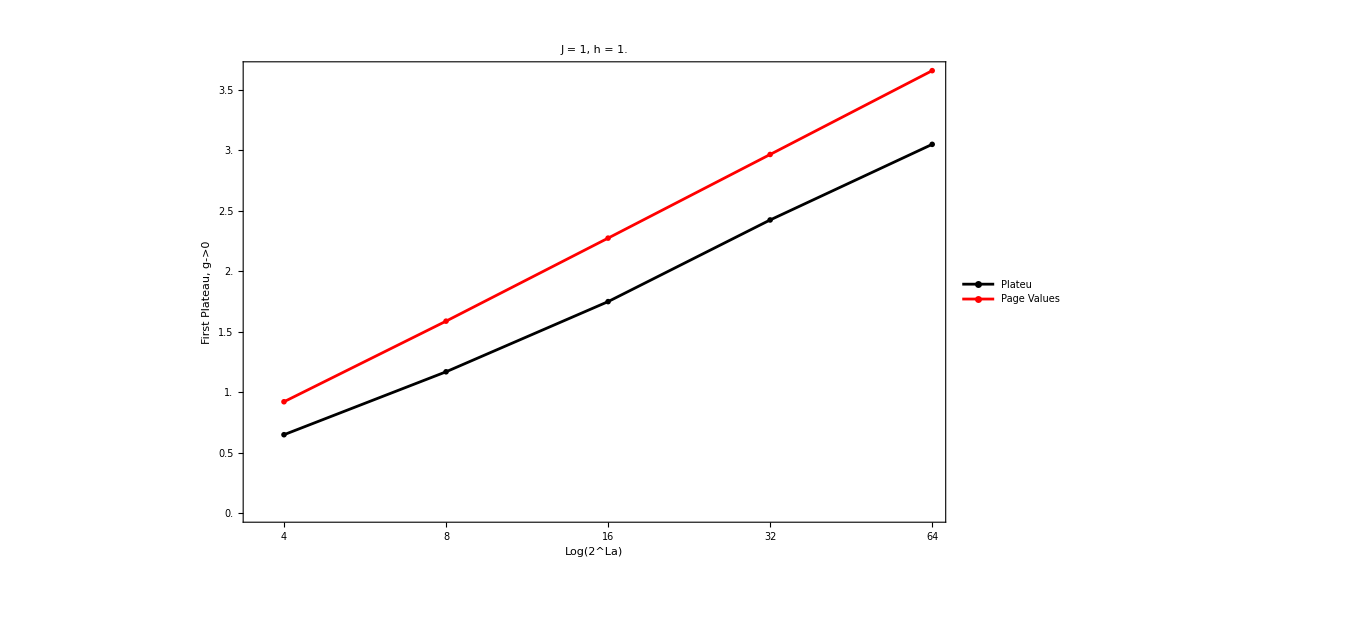

```mathematica
ListLogLinearPlot[{newscaling,pagevalues},PlotStyle->{Directive[Black],Directive[Red]},Joined->True,PlotMarkers->"OpenMarkers",ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["Log(2^La)",25,Black],Style["First Plateau, g->0",25,Black]},PlotLabel->Style["J = "<>ToString[J]<>", h = "<>ToString[N[h]],30,Black],PlotLegends->{Style["Plateu",25],Style["Page Values",25]},Ticks->{{1, 2}, Automatic},PlotRange->All,FrameTicks->{{Range[0,3.75,0.5],None},{Table[2^(i/2),{i,Llist}],None}}]
```

# h -> 0, Plateu

```mathematica
L=10;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=1;
hlist=Table[10^i,{i,-2,-0.5,0.1}];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

17

```mathematica
tlist=Table[10^i,{i,0,3,0.0015}];
tlist//Length
```

2001

```mathematica
c=N[pageEntropy[L/2,L/2]];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
alldata={};
Do[

H=IsingNNOpenHamiltonian[hlist[[h]],g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{h,Length[hlist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-2,-0.5}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.265},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-2,-0.5}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.34},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-2,-0.5}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.365},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-2,-0.5}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.37},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",alldata]
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

plateu_entanglemententropy_halfhaar_L_10_J_1_h_1_g.m

plateu_entanglemententropy_halfhaar_L_10_J_1_h_1_g.png

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.28},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.21},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.165},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.125},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",newalldata]
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",testnorm,ImageResolution->500]
```

plateunorm_entanglemententropy_halfhaar_L_10_J_1_h_1_g.m

plateunorm_entanglemententropy_halfhaar_L_10_J_1_h_1_g.png

```mathematica
scaling={{4,0.265},{6,0.34},{8,0.365},{10,0.37}};
scalingnorm={{4,0.28},{6,0.21},{8,0.165},{10,0.125}};
```

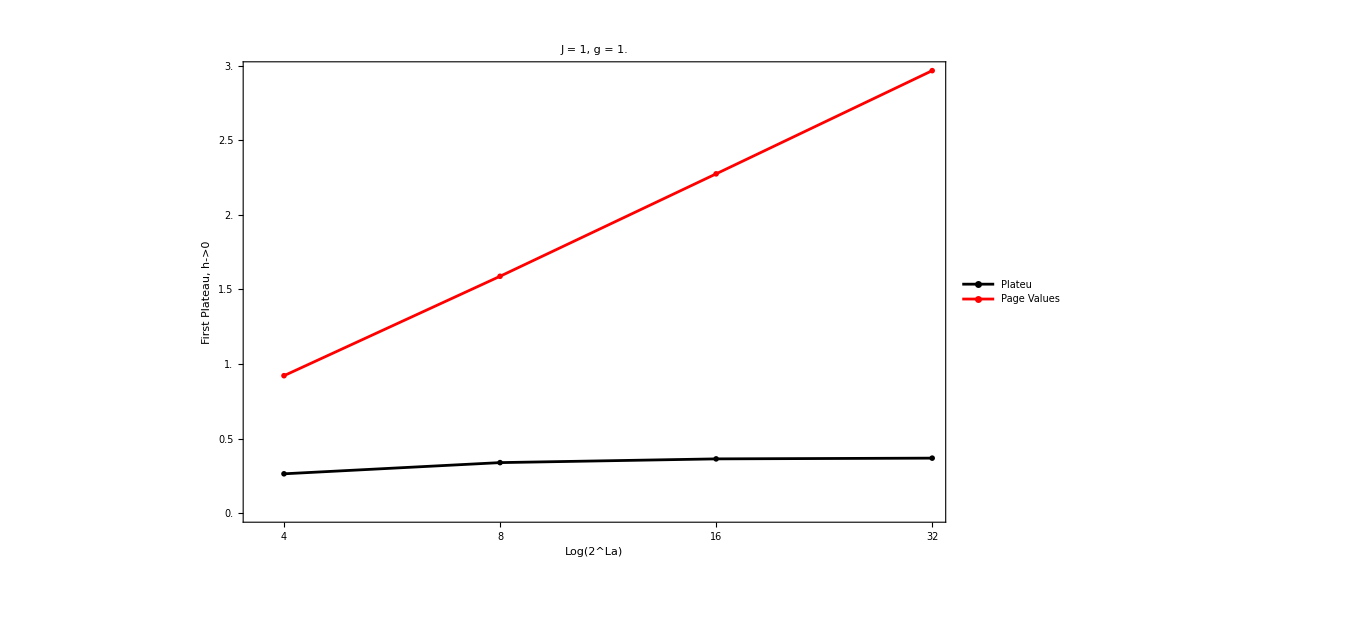

```mathematica
Llist=Range[4,10,2];
newscaling=Table[{2^(Llist[[i]]/2),scaling[[i,2]]},{i,Length[scaling]}];
pagevalues=Table[{2^(i/2),pageEntropy[i/2.,i/2.]},{i,Llist}];
ListLogLinearPlot[{newscaling,pagevalues},PlotStyle->{Directive[Black],Directive[Red]},Joined->True,PlotMarkers->"OpenMarkers",ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["Log(2^La)",25,Black],Style["First Plateau, h->0",25,Black]},PlotLabel->Style["J = "<>ToString[J]<>", g = "<>ToString[N[h]],30,Black],PlotLegends->{Style["Plateu",25],Style["Page Values",25]},Ticks->{{1, 2}, Automatic},PlotRange->All,FrameTicks->{{Range[0,3.75,0.5],None},{Table[2^(i/2),{i,Llist}],None}}]
```

# h=0, Plateu

```mathematica
L=12;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
h=0;
glist=Table[10^i,{i,-3,-1,0.5}];
n=Length[glist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

6

```mathematica
tlist=Table[10^i,{i,0,2,0.0025}];
tlist//Length
```

801

```mathematica
c=N[pageEntropy[L/2,L/2]];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
alldata={};
Do[

H=IsingNNOpenHamiltonian[h,glist[[g]],J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{g,Length[glist]}];
```

```mathematica
(*glist=Table[10^i,{i,-3,-1,0.1}];*)
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.265},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.30},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.35},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.375},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.37},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",alldata]
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

plateu_entanglemententropy_halfhaar_L_12_J_1_h_0_g.m

plateu_entanglemententropy_halfhaar_L_12_J_1_h_0_g.png

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.29},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.19},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.155},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.125},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.105},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",newalldata]
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",testnorm,ImageResolution->500]
```

plateunorm_entanglemententropy_halfhaar_L_12_J_1_h_0_g.m

plateunorm_entanglemententropy_halfhaar_L_12_J_1_h_0_g.png

```mathematica
scaling={{4,0.265},{6,0.30},{8,0.35},{10,0.375},{12,0.37}};
scalingnorm={{4,0.29},{6,0.19},{8,0.155},{10,0.125},{12,0.105}};
```

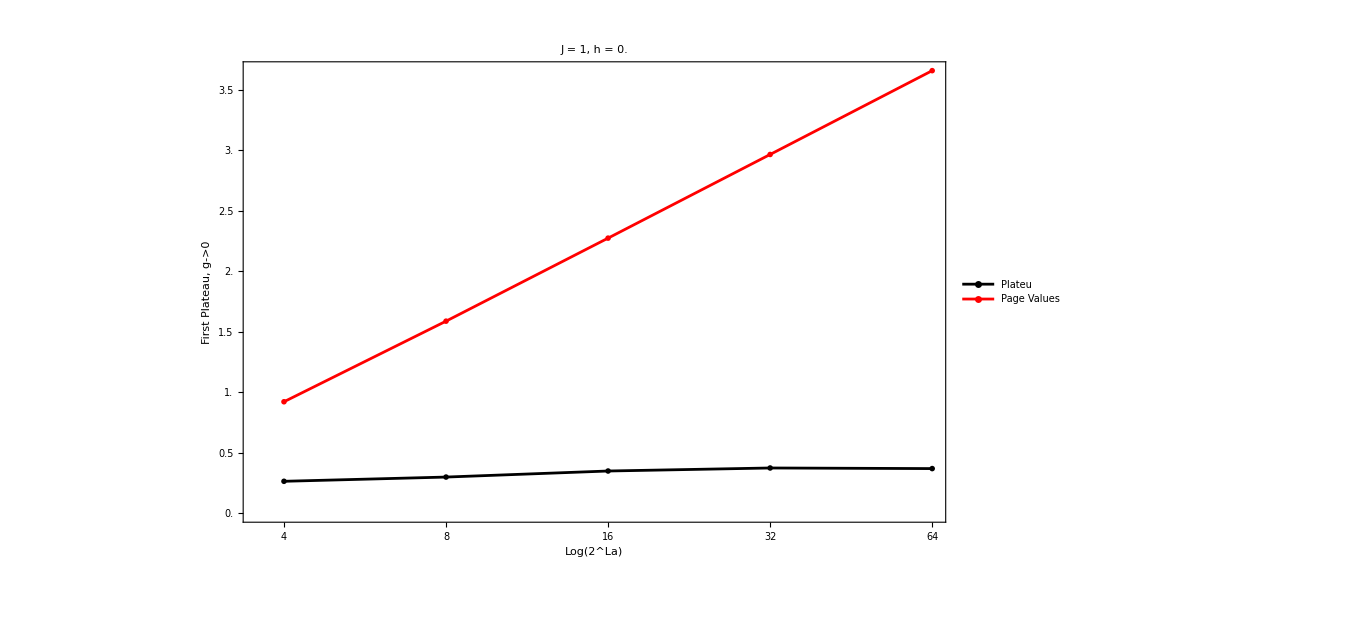

```mathematica
Llist=Range[4,12,2];
newscaling=Table[{2^(Llist[[i]]/2),scaling[[i,2]]},{i,Length[scaling]}];
pagevalues=Table[{2^(i/2),pageEntropy[i/2.,i/2.]},{i,Llist}];
ListLogLinearPlot[{newscaling,pagevalues},PlotStyle->{Directive[Black],Directive[Red]},Joined->True,PlotMarkers->"OpenMarkers",ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["Log(2^La)",25,Black],Style["First Plateau, g->0",25,Black]},PlotLabel->Style["J = "<>ToString[J]<>", h = "<>ToString[N[0]],30,Black],PlotLegends->{Style["Plateu",25],Style["Page Values",25]},Ticks->{{1, 2}, Automatic},PlotRange->All,FrameTicks->{{Range[0,3.75,0.5],None},{Table[2^(i/2),{i,Llist}],None}}]
```

# g=0, Plateu

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0;
hlist=Table[10^i,{i,-3.5,-1,0.2}];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

14

```mathematica
tlist=Table[10^i,{i,1,2.25,0.0015}];
tlist//Length
```

834

```mathematica
c=N[pageEntropy[L/2,L/2]];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
alldata={};
Do[

H=IsingNNOpenHamiltonian[hlist[[h]],g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{h,Length[hlist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,-1}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.275},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,-1}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.345},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,-1}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.35},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,-1}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{c,0.375},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.m",alldata]
Export["plateu_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.png",test,ImageResolution->500]
```

plateu_entanglemententropy_halfhaar_L_10_J_1_g_0_h.m

plateu_entanglemententropy_halfhaar_L_10_J_1_g_0_h.png

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.3},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.215},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.15},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
testnorm=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of "<>ToString[Length[productstatesfull]]<>" Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3,-1}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[{1,0.125},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Black,Dashed]}]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.m",newalldata]
Export["plateunorm_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.png",testnorm,ImageResolution->500]
```

plateunorm_entanglemententropy_halfhaar_L_10_J_1_g_0_h.m

plateunorm_entanglemententropy_halfhaar_L_10_J_1_g_0_h.png

```mathematica
scaling={{4,0.275},{6,0.345},{8,0.35},{10,0.375}};
scalingnorm={{4,0.3},{6,0.215},{8,0.15},{10,0.125}};
```

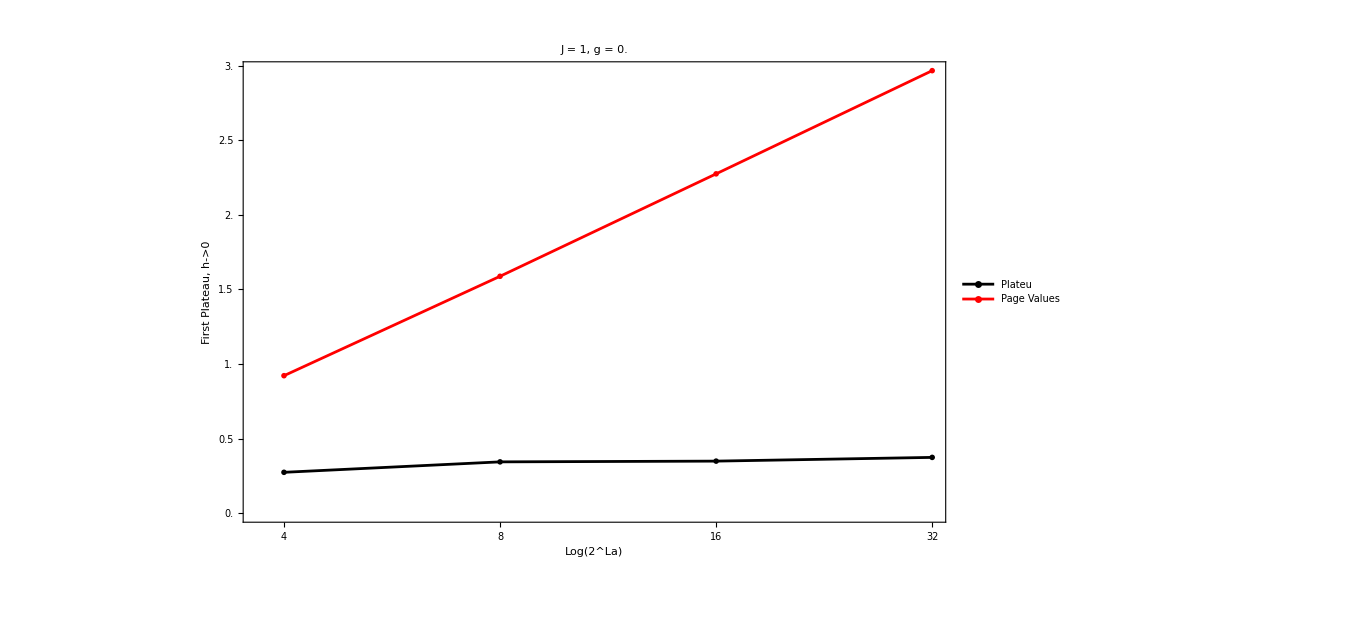

```mathematica
Llist=Range[4,10,2];
newscaling=Table[{2^(Llist[[i]]/2),scaling[[i,2]]},{i,Length[scaling]}];
pagevalues=Table[{2^(i/2),pageEntropy[i/2.,i/2.]},{i,Llist}];
ListLogLinearPlot[{newscaling,pagevalues},PlotStyle->{Directive[Black],Directive[Red]},Joined->True,PlotMarkers->"OpenMarkers",ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["Log(2^La)",25,Black],Style["First Plateau, h->0",25,Black]},PlotLabel->Style["J = "<>ToString[J]<>", g = "<>ToString[N[0]],30,Black],PlotLegends->{Style["Plateu",25],Style["Page Values",25]},Ticks->{{1, 2}, Automatic},PlotRange->All,FrameTicks->{{Range[0,3.75,0.5],None},{Table[2^(i/2),{i,Llist}],None}}]
```